```mathematica
ClearAll["`*"]
RandomVariate[1/8.977893916877134((1+z^2)/(1-z)+(1+(1-z))/z)]
```

RandomVariate::udist: The specification 0.111385 ((2-z)/z+(1+z^2)/(1-z)) is not a random distribution recognized by the system.

RandomVariate[0.111385 ((2-z)/z+(1+z^2)/(1-z))]

```mathematica
Integrate[(1+z^2)/(1-z)+(1+(1-z))/z,{z,80^2/(.5^2*2000^2),1/2}]
```

8.97789

```mathematica
dataQuark=RandomVariate[ProbabilityDistribution[1/8.977893916877134((1+z^2)/(1-z)+(1+(1-z))/z),{z,80^2/(.5^2*2000^2),1/2}],10^6]
```

```mathematica
dataW=RandomVariate[ProbabilityDistribution[2,{z,0,1/2}],10^4];
```

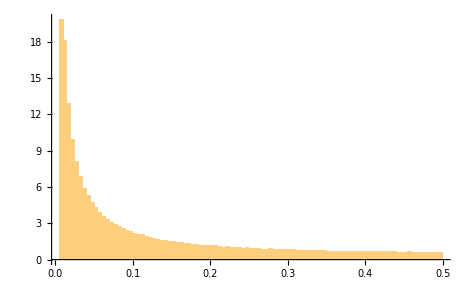

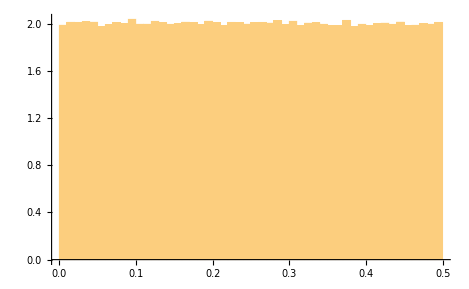

```mathematica
Histogram[dataQuark,100,"ProbabilityDensity",ChartStyle->None]
Histogram[dataW,50,"ProbabilityDensity"]
```

```mathematica
dataW[[1]]
```

0.126787

```mathematica
deltax = 0.5/1000;
nbins= Table[{i*0.5/1000,Length@BinLists[dataW,0.5/1000][[i]]},{i,1000}];
```

```mathematica
AbsoluteTiming[integralemin = Table[{10^ϵ,Sum[*2*Boole[10^(2ϵ)-4*80^2+4 Min[dataW[[1]](1-dataW[[1]]),nbins[[i,1]](1-nbins[[i,1]])]Sqrt[80^2/(dataW[[1]](1-dataW[[1]]))*80^2/(nbins[[i,1]](1-nbins[[i,1]]))]>0],{i,1,Length@nbins}]},{ϵ,.8,1.2,.01}]]
```

{6.72073,{{6.30957,0.002},{6.45654,0.002},{6.60693,0.002},{6.76083,0.002},{6.91831,0.002},{7.07946,0.002},{7.24436,0.002},{7.4131,0.002},{7.58578,0.002},{7.76247,0.002},{7.94328,0.003},{8.12831,0.003},{8.31764,0.004},{8.51138,0.004},{8.70964,0.004},{8.91251,0.004},{9.12011,0.004},{9.33254,0.004},{9.54993,0.004},{9.77237,0.004},{10.,0.004},{10.2329,0.005},{10.4713,0.005},{10.7152,0.006},{10.9648,0.006},{11.2202,0.006},{11.4815,0.006},{11.749,0.006},{12.0226,0.006},{12.3027,0.007},{12.5893,0.008},{12.8825,0.008},{13.1826,0.008},{13.4896,0.008},{13.8038,0.009},{14.1254,0.01},{14.4544,0.01},{14.7911,0.01},{15.1356,0.01},{15.4882,0.011},{15.8489,0.012}}}

{{0.0005,985},{0.001,964},{0.0015,954},{0.002,1019},{0.0025,947},{0.003,968},{0.0035,1002},{0.004,960},{0.0045,1005},{0.005,1012},{0.0055,1021},{0.006,1040},{0.0065,1003},{0.007,969},{0.0075,973},{0.008,1008},{0.0085,980},{0.009,1015},{0.0095,1005},{0.01,1033},{0.0105,981},{0.011,958},{0.0115,975},{0.012,1085},{0.0125,998},{0.013,1008},{0.0135,970},{0.014,1019},{0.0145,959},{0.015,1006},{0.0155,1030},{0.016,1051},{0.0165,1041},{0.017,1038},{0.0175,995},{0.018,1033},{0.0185,986},{0.019,930},{0.0195,1030},{0.02,1008},{0.0205,1016},{0.021,1015},{0.0215,994},{0.022,1020},{0.0225,984},{0.023,970},{0.0235,970},{0.024,1018},{0.0245,1046},{0.025,968},{0.0255,1057},{0.026,1023},{0.0265,1019},{0.027,960},{0.0275,1035},{0.028,975},{0.0285,998},{0.029,1025},{0.0295,954},{0.03,1041},{0.0305,1016},{0.031,1050},{0.0315,994},{0.032,980},{0.0325,960},{0.033,1055},{0.0335,1056},{0.034,986},{0.0345,1026},{0.035,1073},{0.0355,988},{0.036,938},{0.0365,971},{0.037,1031},{0.0375,977},{0.038,978},{0.0385,1028},{0.039,1009},{0.0395,1003},{0.04,1031},{0.0405,957},{0.041,966},{0.0415,995},{0.042,972},{0.0425,1046},{0.043,1048},{0.0435,981},{0.044,1017},{0.0445,1071},{0.045,998},{0.0455,979},{0.046,1044},{0.0465,1007},{0.047,968},{0.0475,1017},{0.048,1012},{0.0485,997},{0.049,1009},{0.0495,1009},{0.05,1020},{0.0505,948},{0.051,1006},{0.0515,938},{0.052,986},{0.0525,1013},{0.053,1014},{0.0535,963},{0.054,1025},{0.0545,993},{0.055,1017},{0.0555,1024},{0.056,1001},{0.0565,1000},{0.057,938},{0.0575,1000},{0.058,921},{0.0585,1003},{0.059,970},{0.0595,977},{0.06,1002},{0.0605,1023},{0.061,1003},{0.0615,984},{0.062,1016},{0.0625,1015},{0.063,995},{0.0635,964},{0.064,1004},{0.0645,984},{0.065,1045},{0.0655,974},{0.066,958},{0.0665,974},{0.067,984},{0.0675,978},{0.068,1014},{0.0685,987},{0.069,958},{0.0695,1034},{0.07,992},{0.0705,1047},{0.071,1012},{0.0715,994},{0.072,1027},{0.0725,981},{0.073,956},{0.0735,1019},{0.074,1002},{0.0745,957},{0.075,1043},{0.0755,999},{0.076,1019},{0.0765,1035},{0.077,969},{0.0775,1002},{0.078,1033},{0.0785,973},{0.079,1009},{0.0795,965},{0.08,1010},{0.0805,990},{0.081,968},{0.0815,1022},{0.082,1042},{0.0825,993},{0.083,974},{0.0835,998},{0.084,1039},{0.0845,991},{0.085,1018},{0.0855,983},{0.086,985},{0.0865,995},{0.087,1001},{0.0875,1006},{0.088,1043},{0.0885,993},{0.089,974},{0.0895,1010},{0.09,947},{0.0905,1047},{0.091,1010},{0.0915,1002},{0.092,1016},{0.0925,1012},{0.093,1081},{0.0935,1038},{0.094,1065},{0.0945,1018},{0.095,974},{0.0955,1026},{0.096,981},{0.0965,992},{0.097,984},{0.0975,1058},{0.098,999},{0.0985,1005},{0.099,1012},{0.0995,1023},{0.1,1019},{0.1005,1008},{0.101,1045},{0.1015,1016},{0.102,982},{0.1025,980},{0.103,975},{0.1035,999},{0.104,1003},{0.1045,1032},{0.105,996},{0.1055,1007},{0.106,1001},{0.1065,1038},{0.107,1002},{0.1075,1011},{0.108,998},{0.1085,975},{0.109,993},{0.1095,956},{0.11,923},{0.1105,951},{0.111,950},{0.1115,1004},{0.112,1042},{0.1125,1037},{0.113,999},{0.1135,960},{0.114,1031},{0.1145,1035},{0.115,1061},{0.1155,964},{0.116,1004},{0.1165,981},{0.117,992},{0.1175,979},{0.118,981},{0.1185,958},{0.119,1009},{0.1195,1028},{0.12,974},{0.1205,994},{0.121,961},{0.1215,1037},{0.122,1040},{0.1225,972},{0.123,1034},{0.1235,1004},{0.124,1022},{0.1245,1015},{0.125,1045},{0.1255,952},{0.126,1016},{0.1265,980},{0.127,1038},{0.1275,1006},{0.128,1026},{0.1285,1060},{0.129,982},{0.1295,1008},{0.13,991},{0.1305,973},{0.131,1004},{0.1315,1054},{0.132,1024},{0.1325,993},{0.133,1027},{0.1335,954},{0.134,986},{0.1345,1045},{0.135,974},{0.1355,987},{0.136,965},{0.1365,1004},{0.137,988},{0.1375,1068},{0.138,1014},{0.1385,1019},{0.139,995},{0.1395,986},{0.14,1001},{0.1405,1000},{0.141,1008},{0.1415,985},{0.142,960},{0.1425,1004},{0.143,1028},{0.1435,970},{0.144,1044},{0.1445,960},{0.145,987},{0.1455,1016},{0.146,998},{0.1465,1040},{0.147,1043},{0.1475,955},{0.148,1012},{0.1485,1026},{0.149,991},{0.1495,941},{0.15,960},{0.1505,990},{0.151,1067},{0.1515,1005},{0.152,984},{0.1525,984},{0.153,1033},{0.1535,951},{0.154,971},{0.1545,969},{0.155,952},{0.1555,1033},{0.156,971},{0.1565,993},{0.157,998},{0.1575,1004},{0.158,1053},{0.1585,1031},{0.159,960},{0.1595,999},{0.16,1014},{0.1605,1007},{0.161,1042},{0.1615,1022},{0.162,1000},{0.1625,1040},{0.163,952},{0.1635,987},{0.164,995},{0.1645,967},{0.165,1027},{0.1655,1040},{0.166,1035},{0.1665,1075},{0.167,994},{0.1675,1065},{0.168,969},{0.1685,972},{0.169,947},{0.1695,996},{0.17,980},{0.1705,980},{0.171,986},{0.1715,1011},{0.172,1019},{0.1725,978},{0.173,982},{0.1735,1005},{0.174,973},{0.1745,956},{0.175,1049},{0.1755,1088},{0.176,990},{0.1765,1012},{0.177,947},{0.1775,985},{0.178,1018},{0.1785,1057},{0.179,957},{0.1795,1057},{0.18,1023},{0.1805,1039},{0.181,1057},{0.1815,1017},{0.182,992},{0.1825,982},{0.183,1007},{0.1835,961},{0.184,980},{0.1845,980},{0.185,1030},{0.1855,934},{0.186,972},{0.1865,1032},{0.187,986},{0.1875,998},{0.188,1005},{0.1885,941},{0.189,965},{0.1895,1005},{0.19,996},{0.1905,1077},{0.191,980},{0.1915,967},{0.192,1019},{0.1925,1046},{0.193,1024},{0.1935,994},{0.194,1030},{0.1945,971},{0.195,1048},{0.1955,987},{0.196,1008},{0.1965,990},{0.197,953},{0.1975,1020},{0.198,990},{0.1985,1035},{0.199,988},{0.1995,983},{0.2,1086},{0.2005,1021},{0.201,989},{0.2015,1046},{0.202,959},{0.2025,988},{0.203,1004},{0.2035,1025},{0.204,1005},{0.2045,988},{0.205,985},{0.2055,1066},{0.206,1006},{0.2065,971},{0.207,1013},{0.2075,972},{0.208,1051},{0.2085,932},{0.209,1014},{0.2095,986},{0.21,1038},{0.2105,1060},{0.211,985},{0.2115,979},{0.212,949},{0.2125,995},{0.213,979},{0.2135,988},{0.214,996},{0.2145,1004},{0.215,989},{0.2155,955},{0.216,963},{0.2165,991},{0.217,1037},{0.2175,968},{0.218,1008},{0.2185,960},{0.219,1027},{0.2195,995},{0.22,971},{0.2205,1058},{0.221,983},{0.2215,1037},{0.222,943},{0.2225,1021},{0.223,1000},{0.2235,1008},{0.224,1050},{0.2245,1038},{0.225,1022},{0.2255,913},{0.226,1020},{0.2265,1027},{0.227,974},{0.2275,1000},{0.228,939},{0.2285,986},{0.229,970},{0.2295,1038},{0.23,1063},{0.2305,990},{0.231,1022},{0.2315,1028},{0.232,961},{0.2325,991},{0.233,995},{0.2335,987},{0.234,1034},{0.2345,1032},{0.235,1054},{0.2355,1001},{0.236,991},{0.2365,981},{0.237,1027},{0.2375,972},{0.238,997},{0.2385,993},{0.239,994},{0.2395,1013},{0.24,995},{0.2405,983},{0.241,985},{0.2415,954},{0.242,1004},{0.2425,1070},{0.243,1016},{0.2435,1062},{0.244,998},{0.2445,960},{0.245,992},{0.2455,989},{0.246,1002},{0.2465,972},{0.247,967},{0.2475,967},{0.248,995},{0.2485,1049},{0.249,961},{0.2495,1018},{0.25,1004},{0.2505,958},{0.251,1035},{0.2515,1033},{0.252,984},{0.2525,1034},{0.253,975},{0.2535,982},{0.254,989},{0.2545,1006},{0.255,988},{0.2555,973},{0.256,1030},{0.2565,1063},{0.257,959},{0.2575,1034},{0.258,976},{0.2585,1012},{0.259,1007},{0.2595,981},{0.26,1030},{0.2605,1027},{0.261,989},{0.2615,1039},{0.262,987},{0.2625,941},{0.263,1015},{0.2635,988},{0.264,986},{0.2645,1023},{0.265,1039},{0.2655,1007},{0.266,1005},{0.2665,993},{0.267,1003},{0.2675,1033},{0.268,1025},{0.2685,1019},{0.269,1026},{0.2695,947},{0.27,996},{0.2705,981},{0.271,1051},{0.2715,996},{0.272,1055},{0.2725,1014},{0.273,1018},{0.2735,1027},{0.274,1073},{0.2745,986},{0.275,1037},{0.2755,1016},{0.276,969},{0.2765,971},{0.277,973},{0.2775,952},{0.278,985},{0.2785,1017},{0.279,951},{0.2795,978},{0.28,989},{0.2805,1045},{0.281,1025},{0.2815,1029},{0.282,1027},{0.2825,1028},{0.283,975},{0.2835,984},{0.284,1031},{0.2845,1018},{0.285,963},{0.2855,1025},{0.286,1005},{0.2865,998},{0.287,1005},{0.2875,988},{0.288,991},{0.2885,1011},{0.289,1027},{0.2895,1056},{0.29,1008},{0.2905,999},{0.291,1078},{0.2915,983},{0.292,978},{0.2925,980},{0.293,1005},{0.2935,1024},{0.294,999},{0.2945,935},{0.295,957},{0.2955,964},{0.296,920},{0.2965,1001},{0.297,1001},{0.2975,985},{0.298,1013},{0.2985,1025},{0.299,978},{0.2995,1035},{0.3,1029},{0.3005,1055},{0.301,975},{0.3015,1055},{0.302,982},{0.3025,1019},{0.303,1037},{0.3035,1017},{0.304,988},{0.3045,1015},{0.305,1054},{0.3055,996},{0.306,986},{0.3065,1026},{0.307,1000},{0.3075,1028},{0.308,1029},{0.3085,985},{0.309,1032},{0.3095,951},{0.31,957},{0.3105,983},{0.311,980},{0.3115,1022},{0.312,957},{0.3125,1000},{0.313,999},{0.3135,1055},{0.314,946},{0.3145,990},{0.315,1058},{0.3155,999},{0.316,918},{0.3165,979},{0.317,996},{0.3175,1004},{0.318,965},{0.3185,998},{0.319,932},{0.3195,1006},{0.32,1032},{0.3205,989},{0.321,958},{0.3215,1078},{0.322,956},{0.3225,983},{0.323,1039},{0.3235,946},{0.324,1035},{0.3245,987},{0.325,1044},{0.3255,1035},{0.326,992},{0.3265,1018},{0.327,1011},{0.3275,1024},{0.328,955},{0.3285,998},{0.329,983},{0.3295,982},{0.33,1022},{0.3305,953},{0.331,1028},{0.3315,1039},{0.332,1032},{0.3325,956},{0.333,963},{0.3335,1053},{0.334,892},{0.3345,1006},{0.335,1020},{0.3355,1036},{0.336,1007},{0.3365,968},{0.337,992},{0.3375,997},{0.338,997},{0.3385,997},{0.339,1016},{0.3395,1057},{0.34,1037},{0.3405,965},{0.341,1033},{0.3415,1033},{0.342,968},{0.3425,1034},{0.343,934},{0.3435,981},{0.344,997},{0.3445,955},{0.345,1000},{0.3455,1009},{0.346,1017},{0.3465,1026},{0.347,998},{0.3475,1045},{0.348,1008},{0.3485,949},{0.349,987},{0.3495,968},{0.35,1026},{0.3505,987},{0.351,961},{0.3515,974},{0.352,1010},{0.3525,949},{0.353,1019},{0.3535,952},{0.354,983},{0.3545,967},{0.355,961},{0.3555,991},{0.356,1059},{0.3565,991},{0.357,998},{0.3575,1014},{0.358,1038},{0.3585,962},{0.359,979},{0.3595,999},{0.36,1003},{0.3605,1020},{0.361,995},{0.3615,1004},{0.362,984},{0.3625,1005},{0.363,932},{0.3635,982},{0.364,993},{0.3645,1027},{0.365,915},{0.3655,1008},{0.366,1001},{0.3665,1014},{0.367,934},{0.3675,995},{0.368,989},{0.3685,989},{0.369,1015},{0.3695,1011},{0.37,1000},{0.3705,1013},{0.371,988},{0.3715,1031},{0.372,1031},{0.3725,983},{0.373,1010},{0.3735,992},{0.374,1013},{0.3745,1015},{0.375,984},{0.3755,1040},{0.376,1045},{0.3765,1018},{0.377,1040},{0.3775,1043},{0.378,1010},{0.3785,1037},{0.379,976},{0.3795,1037},{0.38,952},{0.3805,1001},{0.381,967},{0.3815,962},{0.382,1039},{0.3825,993},{0.383,966},{0.3835,1019},{0.384,958},{0.3845,1022},{0.385,1056},{0.3855,979},{0.386,981},{0.3865,1008},{0.387,936},{0.3875,1042},{0.388,937},{0.3885,963},{0.389,988},{0.3895,943},{0.39,984},{0.3905,1045},{0.391,931},{0.3915,989},{0.392,1052},{0.3925,960},{0.393,1000},{0.3935,990},{0.394,1049},{0.3945,925},{0.395,1030},{0.3955,978},{0.396,1000},{0.3965,1042},{0.397,957},{0.3975,1030},{0.398,974},{0.3985,1011},{0.399,972},{0.3995,1021},{0.4,975},{0.4005,959},{0.401,986},{0.4015,1021},{0.402,1035},{0.4025,980},{0.403,1014},{0.4035,1052},{0.404,912},{0.4045,1031},{0.405,991},{0.4055,1013},{0.406,942},{0.4065,935},{0.407,957},{0.4075,950},{0.408,1070},{0.4085,988},{0.409,992},{0.4095,1028},{0.41,969},{0.4105,981},{0.411,973},{0.4115,1010},{0.412,1017},{0.4125,963},{0.413,1004},{0.4135,1040},{0.414,1006},{0.4145,1048},{0.415,967},{0.4155,980},{0.416,1010},{0.4165,1000},{0.417,1010},{0.4175,1010},{0.418,956},{0.4185,971},{0.419,1015},{0.4195,1020},{0.42,989},{0.4205,959},{0.421,959},{0.4215,981},{0.422,1015},{0.4225,1035},{0.423,949},{0.4235,1033},{0.424,970},{0.4245,1016},{0.425,990},{0.4255,1021},{0.426,990},{0.4265,991},{0.427,1019},{0.4275,1030},{0.428,1024},{0.4285,993},{0.429,982},{0.4295,1077},{0.43,1003},{0.4305,978},{0.431,1005},{0.4315,943},{0.432,1005},{0.4325,991},{0.433,998},{0.4335,969},{0.434,1015},{0.4345,1011},{0.435,1022},{0.4355,996},{0.436,966},{0.4365,1026},{0.437,1015},{0.4375,1036},{0.438,1011},{0.4385,958},{0.439,1049},{0.4395,986},{0.44,946},{0.4405,1065},{0.441,942},{0.4415,972},{0.442,1058},{0.4425,1022},{0.443,1043},{0.4435,1000},{0.444,1042},{0.4445,999},{0.445,1018},{0.4455,1012},{0.446,998},{0.4465,1003},{0.447,1011},{0.4475,961},{0.448,995},{0.4485,1003},{0.449,1002},{0.4495,958},{0.45,1023},{0.4505,1001},{0.451,999},{0.4515,1000},{0.452,974},{0.4525,994},{0.453,969},{0.4535,993},{0.454,1001},{0.4545,1025},{0.455,988},{0.4555,1004},{0.456,978},{0.4565,989},{0.457,994},{0.4575,987},{0.458,966},{0.4585,975},{0.459,947},{0.4595,1054},{0.46,981},{0.4605,963},{0.461,1004},{0.4615,957},{0.462,998},{0.4625,995},{0.463,1024},{0.4635,962},{0.464,1054},{0.4645,1014},{0.465,1044},{0.4655,1013},{0.466,937},{0.4665,1002},{0.467,989},{0.4675,967},{0.468,963},{0.4685,1019},{0.469,998},{0.4695,989},{0.47,958},{0.4705,1000},{0.471,982},{0.4715,1043},{0.472,995},{0.4725,1007},{0.473,1000},{0.4735,1006},{0.474,955},{0.4745,972},{0.475,985},{0.4755,1036},{0.476,1044},{0.4765,965},{0.477,1031},{0.4775,961},{0.478,1021},{0.4785,1000},{0.479,998},{0.4795,1026},{0.48,969},{0.4805,1010},{0.481,999},{0.4815,959},{0.482,1015},{0.4825,1011},{0.483,1011},{0.4835,989},{0.484,985},{0.4845,999},{0.485,1008},{0.4855,1021},{0.486,982},{0.4865,951},{0.487,1025},{0.4875,978},{0.488,1017},{0.4885,989},{0.489,1010},{0.4895,987},{0.49,995},{0.4905,943},{0.491,1004},{0.4915,1001},{0.492,1049},{0.4925,1006},{0.493,970},{0.4935,997},{0.494,985},{0.4945,1008},{0.495,1006},{0.4955,1016},{0.496,1034},{0.4965,1001},{0.497,984},{0.4975,967},{0.498,1058},{0.4985,1040},{0.499,1028},{0.4995,949},{0.5,1042}}

```mathematica
Clear[lengthOfInt]
lengthOfInt[z_,ϵ_]:= Sqrt[1-4a]-Sqrt[1-4b]/.a->z(1-z)/(16*80^4)(4*80^2-ϵ^2)^2/.b->Min[z(16*(1-z))/(1/80^4(4*80^2-ϵ^2)^2),1/4];
```

```mathematica
n=2;
scaling={};
While[n<=5,
dataW=RandomVariate[ProbabilityDistribution[2,{z,0,1/2}],Round[10^n]];
AppendTo[scaling,{10^n,
Mean[Table[
ϵmin = 1;
Do[If[lengthOfInt[dataW[[j]],10^ϵ]>=1/10^n,ϵmin=10^ϵ;Break[]],{ϵ,-1,1.8,0.1}];
ϵmin,
{j,1,Length@dataW}]],StandardDeviation[Table[
ϵmin = 1;
Do[If[lengthOfInt[dataW[[j]],10^ϵ]>=1/10^n,ϵmin=10^ϵ;Break[]],{ϵ,-1,1.8,0.1}];
ϵmin,
{j,1,Length@dataW}]]}];
n+=.5]
```

```mathematica
scaling
```

{{100,13.2077,11.3243},{316.228,8.16438,7.78146},{1000.,4.75638,5.33404},{3162.28,2.71153,3.40139},{10000.,1.47107,1.97372},{31622.8,0.843811,1.22941},{100000.,0.473645,0.710334}}

```mathematica
scalinglog= Log[10,scaling]
fit=LinearModelFit[Table[{scalinglog[[i,1]],scalinglog[[i,2]]},{i,1,Length@scalinglog}],{1,logd},{logd}]
```

{{2,1.12083,1.05401},{2.5,0.911923,0.891061},{3.,0.677277,0.727057},{3.5,0.433215,0.531657},{4.,0.167635,0.295284},{4.5,-0.0737546,0.0896967},{5.,-0.324547,-0.148537}}

FittedModel[2.12036-0.486937 logd]

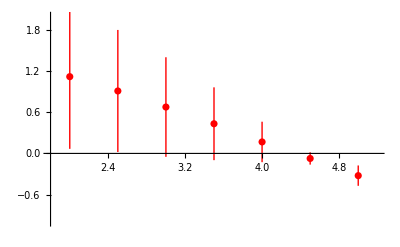

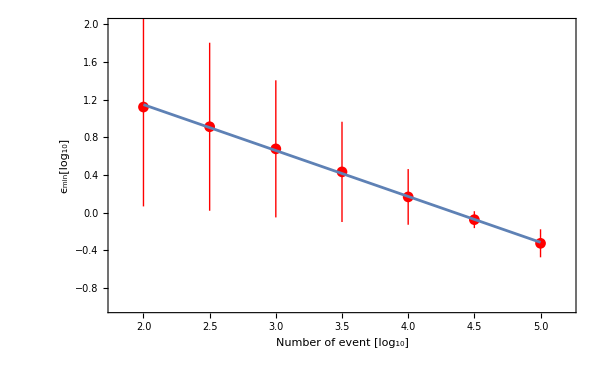

```mathematica
fitplot=Plot[fit[logd],{logd,2,5}];
dataplot=ListPlot[Table[{scalinglog[[i,1]],Around[scalinglog[[i,2]],scalinglog[[i,3]]]},{i,1,Length@scalinglog}],PlotStyle->Red,PlotRange->{{1.8,5.2},{-1,2}}]
Legended[Show[{dataplot,fitplot},ImageSize->600,BaseStyle->Directive[FontFamily->"Modern Computer",16],Frame->True,FrameLabel->{"Number of event [log_10]","ϵ_min[log_10]"}],Placed[Framed[LineLegend[{ColorData[97,"ColorList"][[1]]},{"2.12-0.487 logd"}]],{0.8,.9}]]
```

15.8489

0.367715

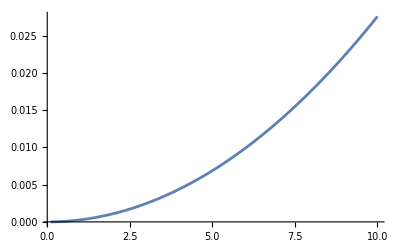

```mathematica
10^1.2
dataW[[1]]
Plot[lengthOfInt[dataW[[1]],x],{x,.1,10}]
```